```mathematica
data=Table[(1+1/i)^i,{i,1000}];
ListPlot[data,PlotRange->{2,2.8},PlotStyle->PointSize[0.01]]
```

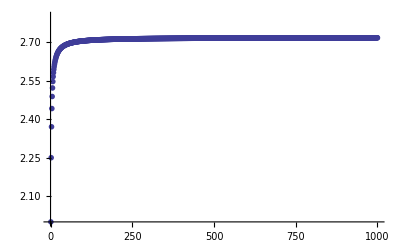
```mathematica
-Graphics-


data=Table[(1+1/i)^i,{i,10}];
ListPlot[data,PlotRange->{2,2.8},PlotStyle->PointSize[0.01]]
```

-Graphics-

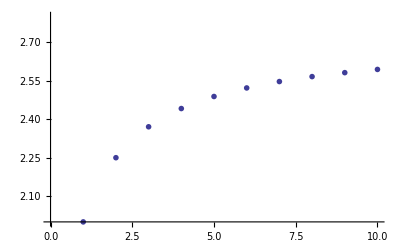

```mathematica
f[x_,y_]:=y+1/(1+x);g[x_]:=x^2+x;xn=1/2;yn=2/3;
For[n=2,n≤10,n++,xN=xn;yN=yn;xn=N[g[xN]];yn=N[f[xN,yN]];Print[yn]];
```

1.33333

1.90476

2.33719

2.58502

2.6605

2.66663

2.66667

2.66667

2.66667

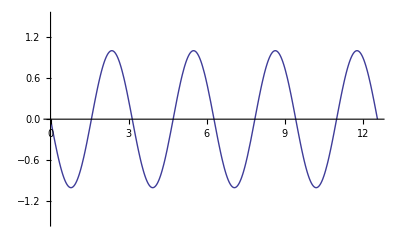

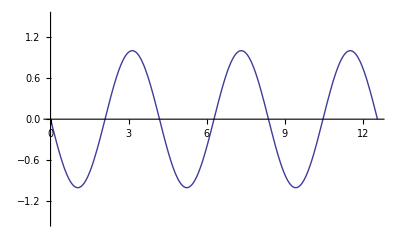

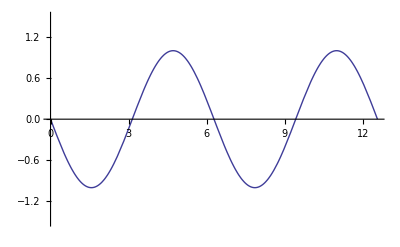

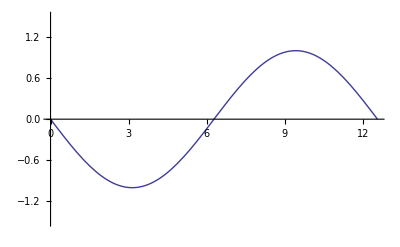

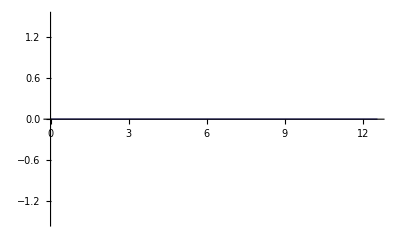

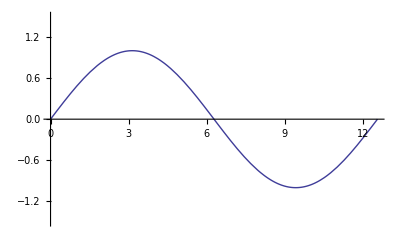

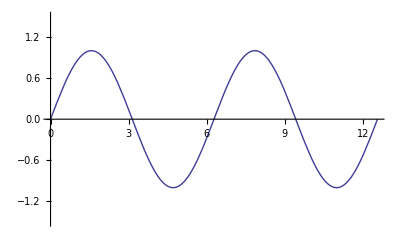

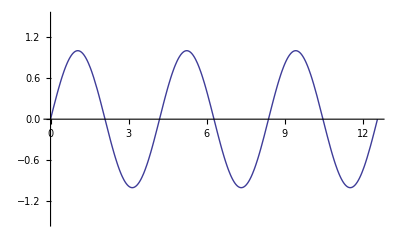

```mathematica
Do [Print[Plot[Sin[c*x],{x,0,4*Pi},PlotRange->{-1.5,1.5}]],{c,-2,2,1/2}]
```

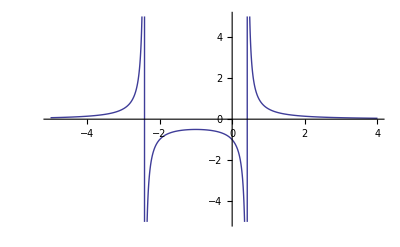

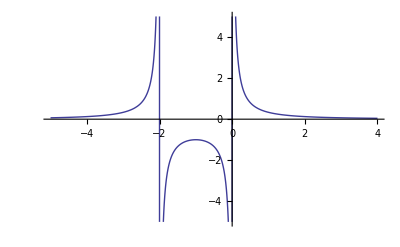

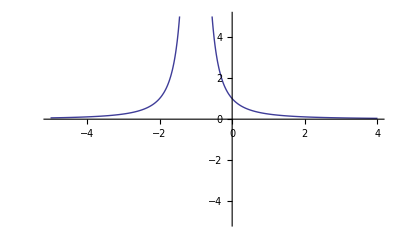

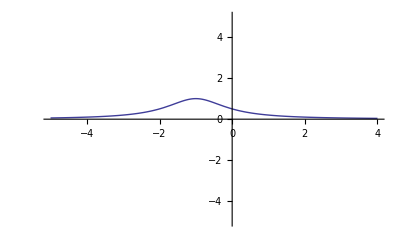

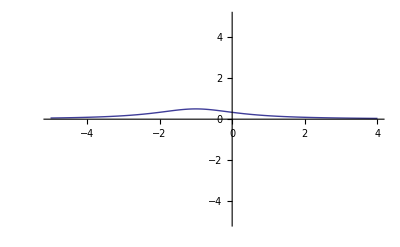

```mathematica
Do [Print[Plot[1/(x^2+2*x+c),{x,-5,4},PlotRange->{-5,5}]],{c,-1,3,1}]
```

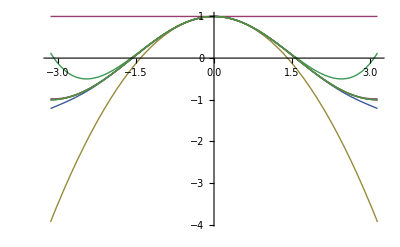

```mathematica
t=Table[Normal[Series[Cos[x],{x,0,i}]],{i,1,13,2}];
PrependTo[t,Cos[x]];
Plot[Evaluate[t],{x,-Pi,Pi}]
```

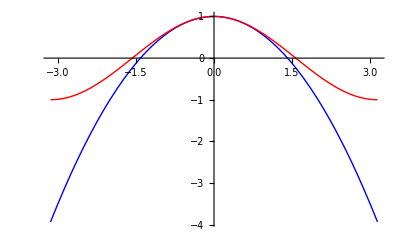

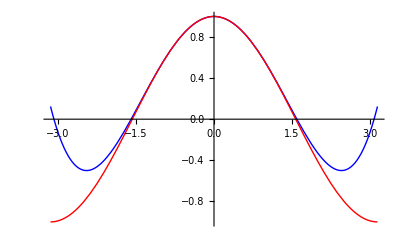

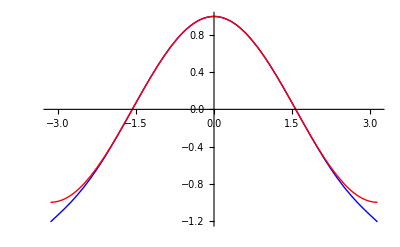

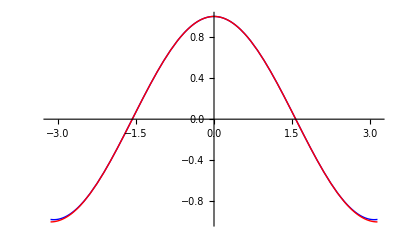

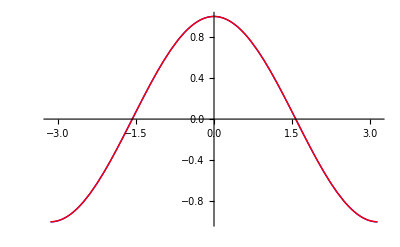

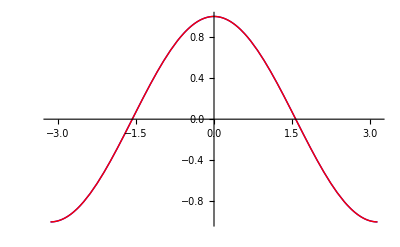

```mathematica
For[i=1,i≤11,a=Normal[Series[Cos[x],{x,0,i}]];Print[Plot[{a,Cos[x]},{x,-Pi,Pi},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}]],i=i+2]
```

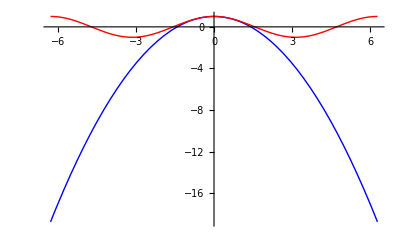

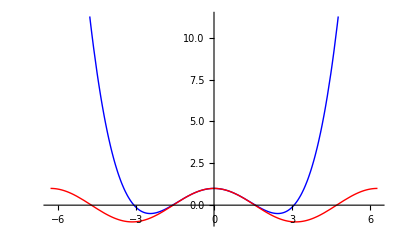

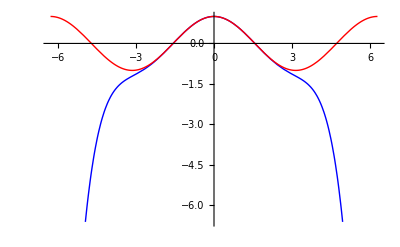

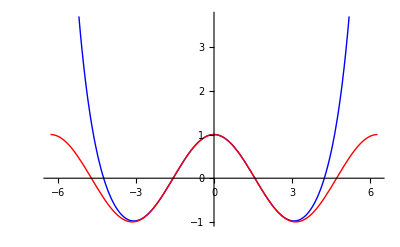

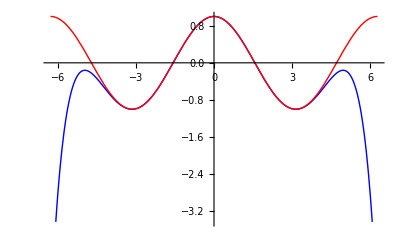

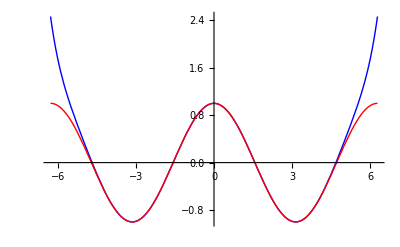

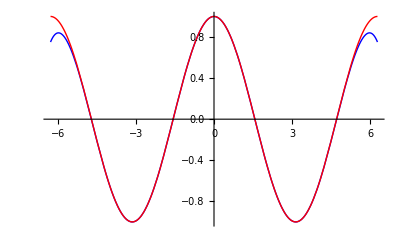

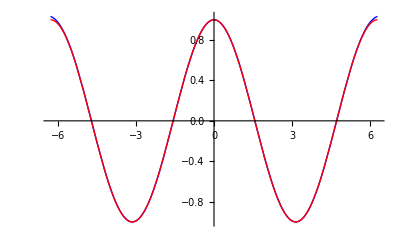

```mathematica
For[i=1,i≤17,a=Normal[Series[Cos[x],{x,0,i}]];Print[Plot[{a,Cos[x]},{x,-2Pi,2Pi},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}]],i=i+2]
```

```mathematica
tt[x0_,n_]:=Normal[Series[Cos[x],{x,x0,n}]];
gs0=tt[0,6];gs3=tt[3,6];gs6=tt[6,6];
Plot[{Cos[x],gs0,gs3,gs6},{x,-3Pi,3Pi},PlotRange->{-2,2},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,1],RGBColor[1,0,0],RGBColor[0,1,0]}]
```

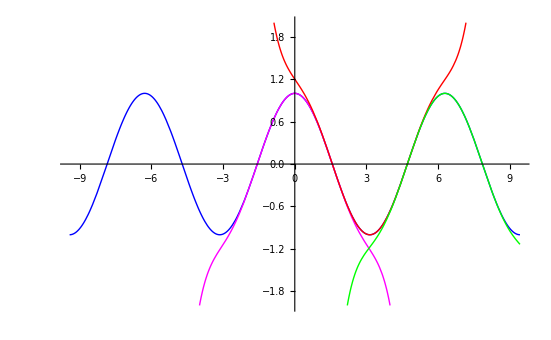

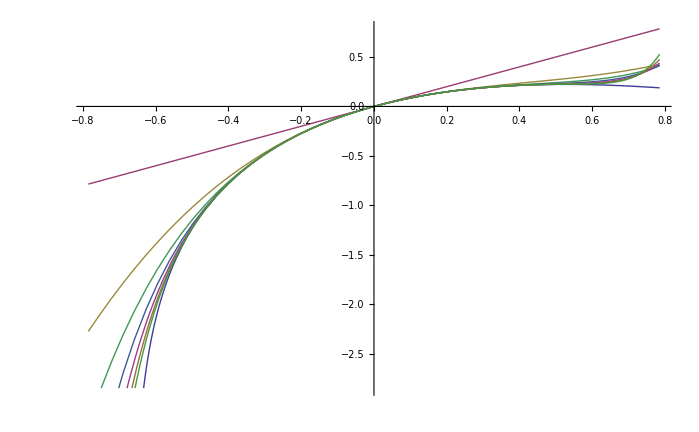

```mathematica
t=Table[Normal[Series[Log[(Cos[x])^2+Sin[x]],{x,0,n}]],{n,1,13,2}];
PrependTo[t,Log[(Cos[x])^2+Sin[x]]];
Print[Plot[Evaluate[t],{x,-Pi/4,Pi/4}]]
```

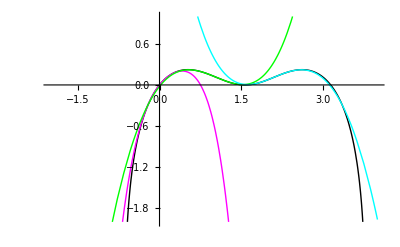

```mathematica
yy[x0_,n_]:=Normal[Series[Log[(Cos[x])^2+Sin[x]],{x,x0,n}]];
gt01=yy[0,4];gt03=yy[-2*Pi/3,4];gt02=yy[-Pi/3,4];gt03=yy[Pi/3,4];gt04=yy[2*Pi/3,4];
Plot[{Log[(Cos[x])^2+Sin[x]],gt01,gt02,gt03,gt04},{x,-2,4},PlotRange->{-2,1},PlotStyle->
{RGBColor[0,0,0],RGBColor[1,0,1],RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,1,1]}]
```

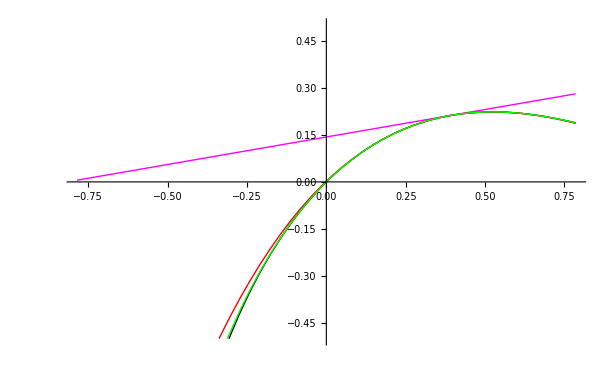

```mathematica
Plot[{Log[(Cos[x])^2+Sin[x]],gt1,gt4,gt7},{x,-Pi/4,Pi/4},PlotRange->{-1/2,1/2},PlotStyle->
{RGBColor[0,0,0],RGBColor[1,0,1],RGBColor[1,0,0],RGBColor[0,1,0]}]
```